### Group Law

The following functions are used to compute sums of points on an elliptic curve.

```mathematica
ellcurve[{a1_,a2_,a3_,a4_,a6_},{x_,y_}]:=y^2+a1*x*y+a3*y-(x^3+a2*x^2+a4*x+a6)
lam[{a1_,a2_,a3_,a4_,a6_},{x1_,y1_},{x2_,y2_}]:=If[x1==x2,(a4+2 a2 x1+3 x1^2-a1*y1)/(2y1+a1*x1+a3),(y2-y1)/(x2-x1)]
nu[{a1_,a2_,a3_,a4_,a6_},{x1_,y1_},{x2_,y2_}]:=If[x1==x2,(-x1^3+a4*x1+2a6-a3*y1)/(2y1+a1*x1+a3),(y1*x2-y2*x1)/(x2-x1)]
x3[{a1_,a2_,a3_,a4_,a6_},{x1_,y1_},{x2_,y2_}]:=lam[{a1,a2,a3,a4,a6},{x1,y1},{x2,y2}]^2+a1*lam[{a1,a2,a3,a4,a6},{x1,y1},{x2,y2}]-a2-x1-x2
y3[{a1_,a2_,a3_,a4_,a6_},{x1_,y1_},{x2_,y2_}]:=-(lam[{a1,a2,a3,a4,a6},{x1,y1},{x2,y2}]+a1)*x3[{a1,a2,a3,a4,a6},{x1,y1},{x2,y2}]-nu[{a1,a2,a3,a4,a6},{x1,y1},{x2,y2}]-a3
ellcurveplus[{a1_,a2_,a3_,a4_,a6_},{x1_,y1_},{x2_,y2_}]:={x3[{a1,a2,a3,a4,a6},{x1,y1},{x2,y2}],y3[{a1,a2,a3,a4,a6},{x1,y1},{x2,y2}]}
aineg[{a1_,a2_,a3_,a4_,a6_},{x_,y_}]:={x,-y-a1*x-a3}
```

```mathematica
ellcurveplusND[ai_,xy1_,xy2_]:=Simplify[ellcurveplus[ai,xy1,xy2],First[xy1]!=First[xy2]]
```

```mathematica
ai = {0,0,0,3,0}
```

{0,0,0,3,0}

We’re going to be working with the following elliptic curve:

```mathematica
ellcurve[ai,{x,y}]
```

-3 x-x^3+y^2

To simplify rational functions in x,y mod the defining equation, we need :

```mathematica
simplifycoefs[coefs_]:=Table[(x^3+3*x)^Floor[i/2]*y^Mod[i,2],{i,0,Length[coefs]-1}].coefs
simplifypolynomial[poly_]:=simplifycoefs[CoefficientList[poly,y]]
ratio[{a_,b_}]:=a/b
simplifyrationalfunc[func_]:=Factor[ratio[Map[simplifypolynomial,NumeratorDenominator[Factor[func]]]]]
simplifyrationalfunclist[list_]:=Map[simplifyrationalfunc,list]
```

Multiplication by i on the elliptic curve is given by:

```mathematica
multbyi[{x_,y_},i_]:={-x,i*y}
```

```mathematica
ellcurve[ai,multbyi[{x,y},I]]+ellcurve[ai,{x,y}]
```

Multiplication-by-2 is given by the duplication formula:

```mathematica
ellcurveplus[ai,{x,y},{x,y}]
```

{-2 x+((3+3 x^2)^2)/(4 y^2),-(3 x-x^3)/(2 y)-((3+3 x^2) (-2 x+((3+3 x^2)^2)/(4 y^2)))/(2 y)}

```mathematica
simplifyrationalfunclist[ellcurveplus[ai,{x,y},{x,y}]]
```

{((-3+x^2)^2)/(4 x (3+x^2)),((-3+x^2) (9+18 x^2+x^4))/(8 x (3+x^2) y)}

```mathematica
dup[{x_,y_}]:={((-3+x^2)^2)/(4 x (3+x^2)),((-3+x^2) (9+18 x^2+x^4))/(8 x (3+x^2) y)}
```

To obtain formula for -2+i, we negate the duplication formula and add i - to obtain the general formula, I’m giong to need to rule out some codimension 1 subvarieties...

```mathematica
Factor[Simplify[ellcurveplus[{0,0,0,3,0},multbyi[{x,y},i],aineg[{0,0,0,3,0},dup[{x,y}]]],First[dup[{x,y}]]!=x&&9+6 x^2+5 x^4!=0]]
```

{(2187 x+8019 x^3+6075 x^5-2997 x^7-999 x^9+225 x^11+33 x^13+x^15-729 y^2+486 x^2 y^2-3888 i x^2 y^2+1053 x^4 y^2-9072 i x^4 y^2+2052 x^6 y^2-2592 i x^6 y^2+1233 x^8 y^2+864 i x^8 y^2+630 x^10 y^2+336 i x^10 y^2+75 x^12 y^2+16 i x^12 y^2+1728 i^2 x^3 y^4+1728 i^2 x^5 y^4+576 i^2 x^7 y^4+64 i^2 x^9 y^4)/(4 x (3+x^2) (9+6 x^2+5 x^4)^2 y^2),(-59049 x-314928 x^3-492075 x^5-69984 x^7+260982 x^9-28998 x^13+864 x^15+675 x^17+48 x^19+x^21+19683 y^2-6561 x^2 y^2+157464 i x^2 y^2-148716 x^4 y^2+629856 i x^4 y^2-207036 x^6 y^2+629856 i x^6 y^2-204606 x^8 y^2-69984 i x^8 y^2-79542 x^10 y^2-143856 i x^10 y^2-16524 x^12 y^2-7776 i x^12 y^2+12132 x^14 y^2+7776 i x^14 y^2+3795 x^16 y^2+864 i x^16 y^2+175 x^18 y^2+24 i x^18 y^2-34992 i x y^4-11664 i x^3 y^4-139968 i^2 x^3 y^4+11664 i x^5 y^4-373248 i^2 x^5 y^4+55728 i x^7 y^4-202176 i^2 x^7 y^4+47088 i x^9 y^4+27216 i x^11 y^4+22464 i^2 x^11 y^4+6960 i x^13 y^4+4608 i^2 x^13 y^4+400 i x^15 y^4+192 i^2 x^15 y^4+41472 i^3 x^4 y^6+55296 i^3 x^6 y^6+27648 i^3 x^8 y^6+6144 i^3 x^10 y^6+512 i^3 x^12 y^6)/(8 x (3+x^2) (9+6 x^2+5 x^4)^3 y^3)}

This is the multiplication by -2+i formula - now, we simplify it as we did earlier to express high powers of y as polynomials in x. We also make sure i^2 is replaced by -1 wherever it appears.

```mathematica
Simplify[simplifyrationalfunclist[{(2187 x+8019 x^3+6075 x^5-2997 x^7-999 x^9+225 x^11+33 x^13+x^15-729 y^2+486 x^2 y^2-3888 i x^2 y^2+1053 x^4 y^2-9072 i x^4 y^2+2052 x^6 y^2-2592 i x^6 y^2+1233 x^8 y^2+864 i x^8 y^2+630 x^10 y^2+336 i x^10 y^2+75 x^12 y^2+16 i x^12 y^2+1728 i^2 x^3 y^4+1728 i^2 x^5 y^4+576 i^2 x^7 y^4+64 i^2 x^9 y^4)/(4 x (3+x^2) (9+6 x^2+5 x^4)^2 y^2),(-59049 x-314928 x^3-492075 x^5-69984 x^7+260982 x^9-28998 x^13+864 x^15+675 x^17+48 x^19+x^21+19683 y^2-6561 x^2 y^2+157464 i x^2 y^2-148716 x^4 y^2+629856 i x^4 y^2-207036 x^6 y^2+629856 i x^6 y^2-204606 x^8 y^2-69984 i x^8 y^2-79542 x^10 y^2-143856 i x^10 y^2-16524 x^12 y^2-7776 i x^12 y^2+12132 x^14 y^2+7776 i x^14 y^2+3795 x^16 y^2+864 i x^16 y^2+175 x^18 y^2+24 i x^18 y^2-34992 i x y^4-11664 i x^3 y^4-139968 i^2 x^3 y^4+11664 i x^5 y^4-373248 i^2 x^5 y^4+55728 i x^7 y^4-202176 i^2 x^7 y^4+47088 i x^9 y^4+27216 i x^11 y^4+22464 i^2 x^11 y^4+6960 i x^13 y^4+4608 i^2 x^13 y^4+400 i x^15 y^4+192 i^2 x^15 y^4+41472 i^3 x^4 y^6+55296 i^3 x^6 y^6+27648 i^3 x^8 y^6+6144 i^3 x^10 y^6+512 i^3 x^12 y^6)/(8 x (3+x^2) (9+6 x^2+5 x^4)^3 y^3)}],i^2==-1]
```

```mathematica
negtwoplusi[{x_,y_},i_]:={(x (3 (81-108 x^2-138 x^4-12 x^6+x^8)+4 i (-81-162 x^2+18 x^6+x^8)))/((9+6 x^2+5 x^4)^2),-1/((9+6 x^2+5 x^4)^3 y)x (3+x^2) (2 (729-1458 x^2-6561 x^4-1404 x^6+999 x^8+78 x^10+x^12)+i (-729-7290 x^2+1053 x^4+8964 x^6+1809 x^8-42 x^10+11 x^12))}
```

We need to replace i by setting it equal to 2 or 3 ; setting it equal to 2 yields:

```mathematica
Factor[PolynomialMod[negtwoplusi[{x,y},2],5],Modulus->5]
```

{x^5,(x^3 (3+x^2)^3)/y}

The x coordinate, as expected, is equal to x^5. The numerator of the y coordinate is the cube of the RHS of the defining equation of E; therefore it is equal to the cube of the LHS of the defining equation of E. Thus, the second term is equal to (y^2)^3/y = y^5, so altogether this shows that we have a lift of Frobenius.

### Elliptic curve points in characteristic 0

We’re going to find the points fixed by - 2 + i on the algebraic model.

I'm going to compute -3+i , since the fixed points of -2+i coincide with kernel of -3+i

```mathematica
Simplify[simplifyrationalfunclist[Factor[ellcurveplusND[ai,negtwoplusimod[{x,y},i],{x,-y}]]],i^2==-1]
```

{((3+x^2) (24 x^2 (729+1215 x^2+1701 x^4+4563 x^6+603 x^8-723 x^10-25 x^12+x^14)+i (-6561-26244 x^4+19440 x^6-34830 x^8-78624 x^10-10836 x^12+1200 x^14+7 x^16)))/(2 x (-81+216 x^2+270 x^4+48 x^6+11 x^8-2 i (-81-162 x^2+18 x^6+x^8))^2),((-9+x^4) (531441+9211644 x^2+13345074 x^4+57395628 x^6+114312303 x^8-1452168 x^10-129729924 x^12-97330248 x^14-23241249 x^16+210060 x^18+429426 x^20+10140 x^22+161 x^24+i (531441-3542940 x^2-13581270 x^4-12990780 x^6-118681929 x^8-223616376 x^10-129135060 x^12-468504 x^14+23384943 x^16+6386580 x^18+358218 x^20-7980 x^22+73 x^24)))/(4 x (81-216 x^2-270 x^4-48 x^6-11 x^8+2 i (-81-162 x^2+18 x^6+x^8))^3 y)}

```mathematica
negthreeplusi[{x_,y_},i_]:={((3+x^2) (24 x^2 (729+1215 x^2+1701 x^4+4563 x^6+603 x^8-723 x^10-25 x^12+x^14)+i (-6561-26244 x^4+19440 x^6-34830 x^8-78624 x^10-10836 x^12+1200 x^14+7 x^16)))/(2 x (-81+216 x^2+270 x^4+48 x^6+11 x^8-2 i (-81-162 x^2+18 x^6+x^8))^2),((-9+x^4) (531441+9211644 x^2+13345074 x^4+57395628 x^6+114312303 x^8-1452168 x^10-129729924 x^12-97330248 x^14-23241249 x^16+210060 x^18+429426 x^20+10140 x^22+161 x^24+i (531441-3542940 x^2-13581270 x^4-12990780 x^6-118681929 x^8-223616376 x^10-129135060 x^12-468504 x^14+23384943 x^16+6386580 x^18+358218 x^20-7980 x^22+73 x^24)))/(4 x (81-216 x^2-270 x^4-48 x^6-11 x^8+2 i (-81-162 x^2+18 x^6+x^8))^3 y)}
```

The poles of this map give us the set of solutions. We’re going to focus on the denominator of the x-coordinate, since the two functions have poles on the same set of points.

```mathematica
First[Last[Transpose[Map[NumeratorDenominator,negthreeplusi[{x,y},i]]]]]
```

2 x (-81+216 x^2+270 x^4+48 x^6+11 x^8-2 i (-81-162 x^2+18 x^6+x^8))^2

The denominator vanishes iff x = 0, or the second term vanishes.

```mathematica
FactorList[First[Last[Transpose[Map[NumeratorDenominator,negthreeplusi[{x,y},i]]]]]][[3,1]]
```

```mathematica
polepoly[x_,i_]:=81-162 i-216 x^2-324 i x^2-270 x^4-48 x^6+36 i x^6-11 x^8+2 i x^8
```

```mathematica
DeleteDuplicates[SolveValues[x*polepoly[x,I]==0&&ellcurve[ai,{x,y}]==0,{x,y}]]
```

{{0,0},{-√(-3+6 ⅈ),-(-3)^(3/4) (-1+2 ⅈ)^(1/4) √2},{-√(-3+6 ⅈ),(-3)^(3/4) (-1+2 ⅈ)^(1/4) √2},{√(-3+6 ⅈ),-(-1)^(1/4) (-1+2 ⅈ)^(1/4) √2 3^(3/4)},{√(-3+6 ⅈ),(-1)^(1/4) (-1+2 ⅈ)^(1/4) √2 3^(3/4)},{-√(-3/5-(6 ⅈ)/5),-√(-4+2 ⅈ) (-1-2 ⅈ)^(1/4) (3/5)^(3/4)},{-√(-3/5-(6 ⅈ)/5),√(-4+2 ⅈ) (-1-2 ⅈ)^(1/4) (3/5)^(3/4)},{√(-3/5-(6 ⅈ)/5),-(-1-2 ⅈ)^(1/4) (3/5)^(3/4) √(4-2 ⅈ)},{√(-3/5-(6 ⅈ)/5),(-1-2 ⅈ)^(1/4) (3/5)^(3/4) √(4-2 ⅈ)}}

We can ‘t plot all of the points in C, but we can plot the image of these points under the double cover E -> P^1 (by plotting their x-coordinates)

```mathematica
Map[ReIm,Map[ComplexExpand,DeleteDuplicates[First[Transpose[DeleteDuplicates[SolveValues[x*polepoly[x,I]==0&&ellcurve[ai,{x,y}]==0,{x,y}]]]]]]]
```

{{0,0},{-√3 5^(1/4) Cos[1/2 (π-ArcTan[2])],-√3 5^(1/4) Sin[1/2 (π-ArcTan[2])]},{√3 5^(1/4) Cos[1/2 (π-ArcTan[2])],√3 5^(1/4) Sin[1/2 (π-ArcTan[2])]},{-(√3 Cos[1/2 (-π+ArcTan[2])])/5^(1/4),-(√3 Sin[1/2 (-π+ArcTan[2])])/5^(1/4)},{(√3 Cos[1/2 (-π+ArcTan[2])])/5^(1/4),(√3 Sin[1/2 (-π+ArcTan[2])])/5^(1/4)}}

This shows the image of the F5 points on y^2 = x^3 + 3x under the double cover E - > P^2

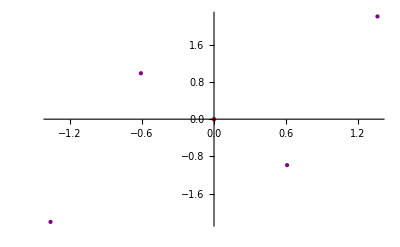

```mathematica
Show[ListPlot[Map[ReIm,Map[ComplexExpand,DeleteDuplicates[First[Transpose[DeleteDuplicates[SolveValues[x*polepoly[x,I]==0&&ellcurve[ai,{x,y}]==0,{x,y}]]]]]]],PlotStyle->Directive[{PointSize[Large],Purple}]],Graphics[{Red,PointSize[Large],Point[{0,0}]}]]
```

Note that the purple points have two points in their preimage, and the red point has only one point in its preimage, giving a total of 9 points not at infinity

We compare to the reduction mod 5 - so we’re first going to look for all solutions to the equation mod 5

```mathematica
Select[Tuples[Table[i,{i,-2,2}],2],Mod[ellcurve[ai,#],5]==0&]
```

{{-2,-1},{-2,1},{-1,-1},{-1,1},{0,0},{1,-2},{1,2},{2,-2},{2,2}}

```mathematica
Length[Select[Tuples[Table[i,{i,-2,2}],2],Mod[ellcurve[ai,#],5]==0&]]
```

9

9 points as expected - we plot them on F5 x F5, using -2,2 as the bounds for the fundamental domain to obtain a more symmetric picture

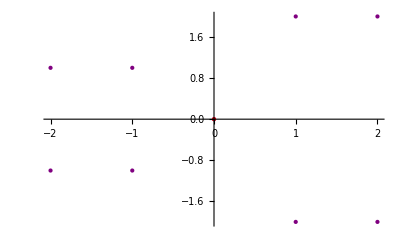

```mathematica
Show[ListPlot[Select[Tuples[Table[i,{i,-2,2}],2],Mod[ellcurve[ai,#],5]==0&],PlotStyle->Directive[{PointSize[Large],Purple}]],Graphics[{Red,PointSize[Large],Point[{0,0}]}]]
```

### F_25 points on algebraic curve in characteristic 0

We can do something similar to find the F_25 points on the algebraic elliptic curve in characteristic 0.

```mathematica
Factor[negtwoplusi[negtwoplusi[{x,y},I],I]]
```

```mathematica
twoplusiSq[{x_,y_}]:={(x ((3+6 ⅈ)+x^2)^2 ((243+486 ⅈ)-(1539+648 ⅈ) x^2-(2970+540 ⅈ) x^4-(414+648 ⅈ) x^6+(135-90 ⅈ) x^8+x^10)^2)/((3+(1+2 ⅈ) x^2)^2 (243+(3645-2430 ⅈ) x^2-(1242+1944 ⅈ) x^4-(990+180 ⅈ) x^6-(57+24 ⅈ) x^8+(1+2 ⅈ) x^10)^2),-((((3+6 ⅈ)+x^2) (9-(6+24 ⅈ) x^2+x^4) ((243+486 ⅈ)-(1539+648 ⅈ) x^2-(2970+540 ⅈ) x^4-(414+648 ⅈ) x^6+(135-90 ⅈ) x^8+x^10) (59049-(3346110-2361960 ⅈ) x^2-(13981491+1259712 ⅈ) x^4-(5021352+4968864 ⅈ) x^6+(1739394-5458752 ⅈ) x^8+(1074060-3184272 ⅈ) x^10+(193266-606528 ⅈ) x^12-(61992+61344 ⅈ) x^14-(19179+1728 ⅈ) x^16-(510-360 ⅈ) x^18+x^20) y)/((3+(1+2 ⅈ) x^2)^3 (243+(3645-2430 ⅈ) x^2-(1242+1944 ⅈ) x^4-(990+180 ⅈ) x^6-(57+24 ⅈ) x^8+(1+2 ⅈ) x^10)^3))}
```

```mathematica
simplifyrationalfunclist[Factor[ellcurveplusND[ai,twoplusiSq[{x,y}],{x,-y}]]]
```

{-((-3+x^2)^2 (81+(324-864 ⅈ) x^2+(342-576 ⅈ) x^4+(36-96 ⅈ) x^6+x^8)^2)/(4 x (3+x^2) ((3-6 ⅈ)+x^2)^2 (3 ⅈ+(2+ⅈ) x^2)^2 (9-(6-24 ⅈ) x^2+x^4)^2),((-3+x^2) (9+18 x^2+x^4) (81+(324-864 ⅈ) x^2+(342-576 ⅈ) x^4+(36-96 ⅈ) x^6+x^8) (6561-(87480-279936 ⅈ) x^2+(253692-186624 ⅈ) x^4+(243000-31104 ⅈ) x^6+(119718+41472 ⅈ) x^8+(27000-3456 ⅈ) x^10+(3132-2304 ⅈ) x^12-(120-384 ⅈ) x^14+x^16) y)/(8 x^2 (3+x^2)^2 ((3-6 ⅈ)+x^2)^3 (3+(1-2 ⅈ) x^2)^3 (9-(6-24 ⅈ) x^2+x^4)^3)}

```mathematica
twoplusiSqminus1[{x_,y_}]:={-((-3+x^2)^2 (81+(324-864 ⅈ) x^2+(342-576 ⅈ) x^4+(36-96 ⅈ) x^6+x^8)^2)/(4 x (3+x^2) ((3-6 ⅈ)+x^2)^2 (3 ⅈ+(2+ⅈ) x^2)^2 (9-(6-24 ⅈ) x^2+x^4)^2),((-3+x^2) (9+18 x^2+x^4) (81+(324-864 ⅈ) x^2+(342-576 ⅈ) x^4+(36-96 ⅈ) x^6+x^8) (6561-(87480-279936 ⅈ) x^2+(253692-186624 ⅈ) x^4+(243000-31104 ⅈ) x^6+(119718+41472 ⅈ) x^8+(27000-3456 ⅈ) x^10+(3132-2304 ⅈ) x^12-(120-384 ⅈ) x^14+x^16) y)/(8 x^2 (3+x^2)^2 ((3-6 ⅈ)+x^2)^3 (3+(1-2 ⅈ) x^2)^3 (9-(6-24 ⅈ) x^2+x^4)^3)}
```

```mathematica
FullSimplify[DeleteDuplicates[SolveValues[Denominator[First[twoplusiSqminus1[{x,y}]]]==0&&ellcurve[ai,{x,y}]==0,{x,y}]]]
```

{{0,0},{-√(-3+6 ⅈ),(1-ⅈ) (-1+2 ⅈ)^(1/4) 3^(3/4)},{-√(-3+6 ⅈ),(-1+ⅈ) (-1+2 ⅈ)^(1/4) 3^(3/4)},{√(-3+6 ⅈ),(-1-ⅈ) (-1+2 ⅈ)^(1/4) 3^(3/4)},{√(-3+6 ⅈ),(1+ⅈ) (-1+2 ⅈ)^(1/4) 3^(3/4)},{-√(-3/5-(6 ⅈ)/5),Root-1.19-1.30 ⅈRoot[11664+2376 #1^4+125 #1^8&,3]-1.189307808022884},{-√(-3/5-(6 ⅈ)/5),√(-4+2 ⅈ) (-1-2 ⅈ)^(1/4) (3/5)^(3/4)},{√(-3/5-(6 ⅈ)/5),-(-11-2 ⅈ)^(1/4) (3/5)^(3/4) √2},{√(-3/5-(6 ⅈ)/5),(-11-2 ⅈ)^(1/4) (3/5)^(3/4) √2},{-ⅈ √3,0},{ⅈ √3,0},{-√((3-12 ⅈ)-6 √(-4-2 ⅈ)),ⅈ 3^(3/4) √((4+12 ⅈ)-2 √(-31+22 ⅈ))},{-√((3-12 ⅈ)-6 √(-4-2 ⅈ)),√(-6 √(3 ((-63+46 ⅈ)+4 √(116-362 ⅈ))))},{√((3-12 ⅈ)-6 √(-4-2 ⅈ)),-3^(3/4) √((4+12 ⅈ)-2 √(-31+22 ⅈ))},{√((3-12 ⅈ)-6 √(-4-2 ⅈ)),3^(3/4) √((4+12 ⅈ)-2 √(-31+22 ⅈ))},{-√((3-12 ⅈ)+6 √(-4-2 ⅈ)),-3^(3/4) √(2 ((2+6 ⅈ)+√(-31+22 ⅈ)))},{-√((3-12 ⅈ)+6 √(-4-2 ⅈ)),3^(3/4) √(2 ((2+6 ⅈ)+√(-31+22 ⅈ)))},{√((3-12 ⅈ)+6 √(-4-2 ⅈ)),ⅈ 3^(3/4) √(2 ((2+6 ⅈ)+√(-31+22 ⅈ)))},{√((3-12 ⅈ)+6 √(-4-2 ⅈ)),√(-6 √(3 ((-63+46 ⅈ)-4 √(116-362 ⅈ))))}}

```mathematica
pts25complexplanexvalues=DeleteDuplicates[Map[ReIm,Map[ComplexExpand,First[Transpose[FullSimplify[DeleteDuplicates[SolveValues[Denominator[First[twoplusiSqminus1[{x,y}]]]==0&&ellcurve[ai,{x,y}]==0,{x,y}]]]]]]]]
```

We plot the x-values of the points in the complex plane as above.

Note that we now have 3 branch points, at x = 0, x= sqrt(-3) and x = -sqrt(-3)

We also have 8 other points which are not branch points; altogether, this gives 3+ 2*8 = 19 noninfinite points, so 20 points altogether.

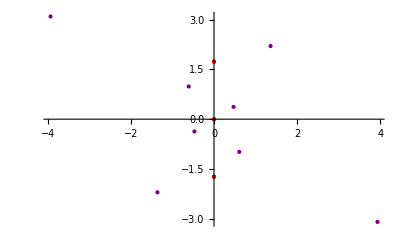

```mathematica
Show[ListPlot[pts25complexplanexvalues,PlotStyle->Directive[{PointSize[Large],Purple}]],ListPlot[{{0,0},{0,Sqrt[3]},{0,-Sqrt[3]}},PlotStyle->Directive[{PointSize[Large],Red}]]]
```

### F_25 points mod 5

To go along with this picture, we can find the F_25 points mod 5.

Note - since sqrt(-3) is one of the points on the curve, we will represent F_25 as F_5 + F_5 sqrt(-3); the 3 branch points therefore have coordinates (0, 0), (0,1) (0,-1)

```mathematica
f25sqrtneg3 = {{0,-3},{1,0}}
f25elts=Table[First[Tuples[Table[i,{i,0,4}],2][[j]]]*IdentityMatrix[2]+Last[Tuples[Table[i,{i,0,4}],2][[j]]]*f25sqrtneg3,{j,1,25}]
```

{{0,-3},{1,0}}

{{{0,0},{0,0}},{{0,-3},{1,0}},{{0,-6},{2,0}},{{0,-9},{3,0}},{{0,-12},{4,0}},{{1,0},{0,1}},{{1,-3},{1,1}},{{1,-6},{2,1}},{{1,-9},{3,1}},{{1,-12},{4,1}},{{2,0},{0,2}},{{2,-3},{1,2}},{{2,-6},{2,2}},{{2,-9},{3,2}},{{2,-12},{4,2}},{{3,0},{0,3}},{{3,-3},{1,3}},{{3,-6},{2,3}},{{3,-9},{3,3}},{{3,-12},{4,3}},{{4,0},{0,4}},{{4,-3},{1,4}},{{4,-6},{2,4}},{{4,-9},{3,4}},{{4,-12},{4,4}}}

```mathematica
eqmat[{xmat_,ymat_}]:=MatrixPower[xmat,3]+3*xmat-MatrixPower[ymat,2]
```

```mathematica
Mod[Select[Tuples[f25elts,2],Mod[eqmat[#],5]=={{0,0},{0,0}}&],5]
```

{{{{0,0},{0,0}},{{0,0},{0,0}}},{{{0,2},{1,0}},{{0,0},{0,0}}},{{{0,3},{4,0}},{{0,0},{0,0}}},{{{1,0},{0,1}},{{2,0},{0,2}}},{{{1,0},{0,1}},{{3,0},{0,3}}},{{{1,4},{2,1}},{{1,3},{4,1}}},{{{1,4},{2,1}},{{4,2},{1,4}}},{{{1,1},{3,1}},{{1,2},{1,1}}},{{{1,1},{3,1}},{{4,3},{4,4}}},{{{2,0},{0,2}},{{2,0},{0,2}}},{{{2,0},{0,2}},{{3,0},{0,3}}},{{{3,0},{0,3}},{{1,0},{0,1}}},{{{3,0},{0,3}},{{4,0},{0,4}}},{{{4,0},{0,4}},{{1,0},{0,1}}},{{{4,0},{0,4}},{{4,0},{0,4}}},{{{4,4},{2,4}},{{2,4},{2,2}}},{{{4,4},{2,4}},{{3,1},{3,3}}},{{{4,1},{3,4}},{{2,1},{3,2}}},{{{4,1},{3,4}},{{3,4},{2,3}}}}

```mathematica
firstcol[m_]:=First[Transpose[m]]
```

```mathematica
mat2pt[m_]:=firstcol[m].{1,Sqrt[-3]}
matpair2ptpair[{m1_,m2_}]:=Map[mat2pt,{m1,m2}]
```

```mathematica
tosymfd[n_]:=If[Mod[n,5]<3,Mod[n,5],Mod[n,5]-5]
tosymfdList[l_]:=Map[tosymfd,l]
tosymfdMat[m_]:=Map[tosymfdList,m]
tosymfdMatPair[ms_]:=Map[tosymfdMat,ms]
```

```mathematica
Map[matpair2ptpair,Map[tosymfdMatPair,Mod[Select[Tuples[f25elts,2],Mod[eqmat[#],5]=={{0,0},{0,0}}&],5]]]
```

{{0,0},{ⅈ √3,0},{-ⅈ √3,0},{1,2},{1,-2},{1+2 ⅈ √3,1-ⅈ √3},{1+2 ⅈ √3,-1+ⅈ √3},{1-2 ⅈ √3,1+ⅈ √3},{1-2 ⅈ √3,-1-ⅈ √3},{2,2},{2,-2},{-2,1},{-2,-1},{-1,1},{-1,-1},{-1+2 ⅈ √3,2+2 ⅈ √3},{-1+2 ⅈ √3,-2-2 ⅈ √3},{-1-2 ⅈ √3,2-2 ⅈ √3},{-1-2 ⅈ √3,-2+2 ⅈ √3}}

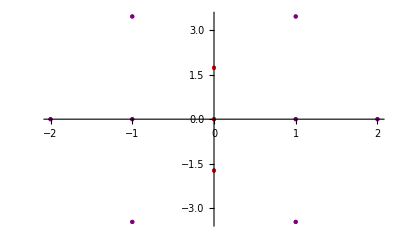

```mathematica
Show[ListPlot[Map[ReIm,firstcol[Map[matpair2ptpair,Map[tosymfdMatPair,Mod[Select[Tuples[f25elts,2],Mod[eqmat[#],5]=={{0,0},{0,0}}&],5]]]]],PlotStyle->Directive[{PointSize[Large],Purple}]],ListPlot[{{0,0},{0,Sqrt[3]},{0,-Sqrt[3]}},PlotStyle->Directive[{PointSize[Large],Red}]]]
```